```mathematica
(* This notebook analyzes the dynamics of NNC and BBC estimates of the FPR of the RF monitor depending on the window size (d). *)
```

```mathematica
(*** APPROACH ESTIMATES ***)
```

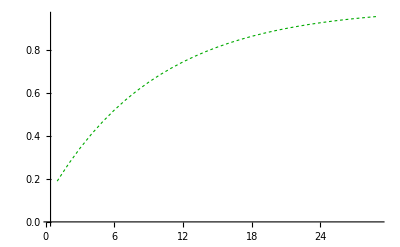

```mathematica
(* ECC *) 
gtRfFPRChart =ListLinePlot[ {#, Simplify@predRfMonFPRTheor[0.1, #]}& /@ Table[n, {n,1,29, 1}], 
PlotStyle->{Dashing[0.005],Darker@Green, Thickness[0.002]}(*PlotStyle->Green*), (*PlotLegends->{"Ground-truth FPR"},*) PlotRange->All]
```

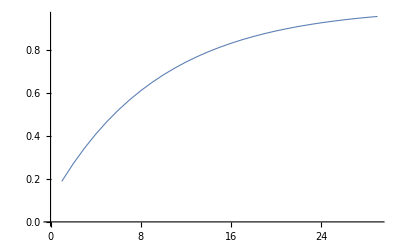

```mathematica
(* NCC; estimatd Pl detector FNR = 0.09959699010793902 *) 
predRfFNRchartSesh4567 = ListLinePlot[Inner[List, Range[1,29], predRfMonFPRTheor[countFromFiles[ "FNcount",detFilenames[fullStatelessTripleListNoRedun[{4,5,6,7}]]]/countFromFiles[ "h1count",detFilenames[fullStatelessTripleListNoRedun[{4,5,6,7}]]],#]&/@ Range[1,29], List], PlotStyle->{ColorData[97,"ColorList"][[1]],Thickness[0.002](*Darker@Magenta,Dashed*)}(*, PlotLegends->{"Our prediction (7.7 hrs)"}*)]
```

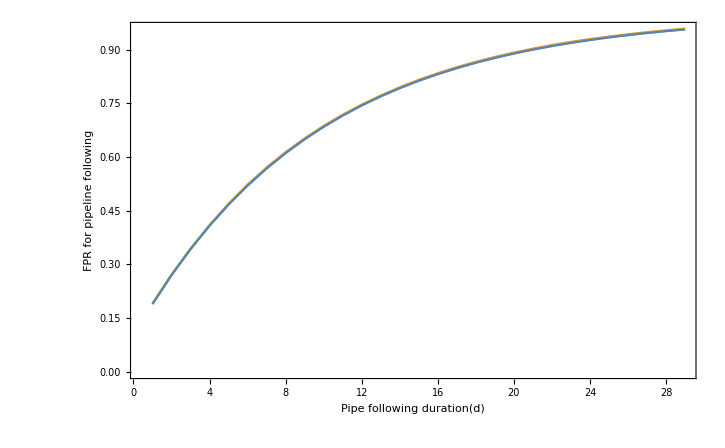

```mathematica
(* COMBINED CHART *) 
Show[gtRfFPRChart,estRfFNRChartSesh4567, predRfFNRchartSesh4567,(*PlotLabel->"Bhah",  AxesLabel -> {"Monitor window size", "Monitor FPR"}*)Frame->True, FrameLabel->{StringJoin["Pipe following duration", ToString[ Style["(d)", Italic], StandardForm] ],"FPR for pipeline following"}, ImageSize->500, BaseStyle-> {FontSize->15}]
```

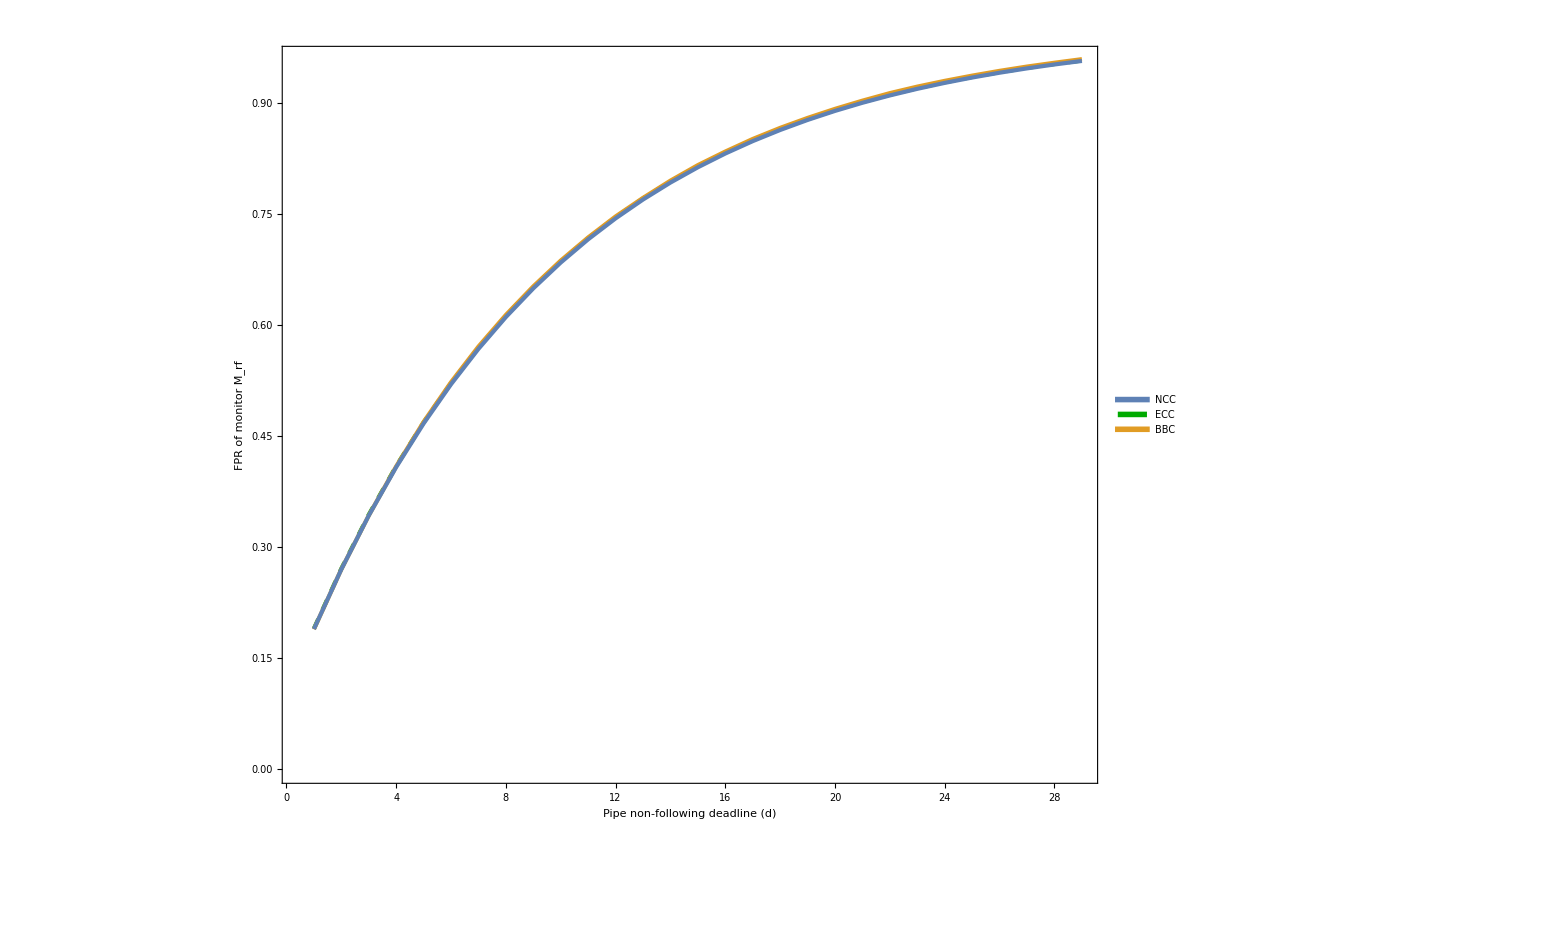

```mathematica
(* PRODUCTION FIGURE *) 
Legended[Show[gtRfFPRChart,estRfFNRChartSesh4567, predRfFNRchartSesh4567,(*PlotLabel->"Bhah",  AxesLabel -> {"Monitor window size", "Monitor FPR"}*)Frame->True, FrameLabel->{StringJoin["Pipe non-following deadline ", ToString[ Style["(d)", Italic], StandardForm] ],StringJoin["FPR of monitor ", ToString[Style[Subscript[ "M", "rf"],Italic], StandardForm]]}, ImageSize->1500, BaseStyle-> {FontSize->35}],Placed[LineLegend[Directive@@@{{ColorData[97,"ColorList"][[1]],AbsoluteThickness[5]},{AbsoluteDashing[10],AbsoluteThickness[5],Darker@Green} , {ColorData[97,"ColorList"][[2]],AbsoluteThickness[5]}},{"NCC","ECC", "BBC"}
(*, LegendMarkers->Graphics[{ Thickness[0.3],Line[{{-10,0},{10,0}}]}]*)(*LegendMarkers->Automatic*)],{0.1,0.85}]]
```

```mathematica
(** RMSE ESTIMATES ON FULL DATASET FOR NCC AND BBC **) 
 eccRfEsts = Simplify@predRfMonFPRTheor[0.1, #]& /@ Table[n, {n,1,29, 1}]
```

{0.19,0.271,0.3439,0.40951,0.468559,0.521703,0.569533,0.61258,0.651322,0.686189,0.71757,0.745813,0.771232,0.794109,0.814698,0.833228,0.849905,0.864915,0.878423,0.890581,0.901523,0.911371,0.920234,0.92821,0.935389,0.94185,0.947665,0.952899,0.957609}

```mathematica
bbcRfEsts = getMonValues[dataDirPathForSeshNumPostCorr[All], "FPR",11]
```

{0.189048,0.270127,0.342801,0.409231,0.469308,0.523021,0.571181,0.613939,0.652491,0.687322,0.7186,0.746941,0.772036,0.795329,0.816313,0.834639,0.851623,0.866614,0.880062,0.892301,0.903391,0.913582,0.922356,0.930144,0.937203,0.943659,0.949452,0.954618,0.959474}

```mathematica
nccRfEsts = N@predRfMonFPRTheor[countFromFiles[ "FNcount",detFilenames[fullStatelessTripleListNoRedun[{4,5,6,7}]]]/countFromFiles[ "h1count",detFilenames[fullStatelessTripleListNoRedun[{4,5,6,7}]]],#]&/@ Range[1,29]
```

{0.189224,0.269952,0.342642,0.408094,0.467029,0.520097,0.56788,0.610906,0.649647,0.684532,0.715942,0.744226,0.769693,0.792624,0.813272,0.831865,0.848606,0.86368,0.877253,0.889475,0.90048,0.910389,0.919311,0.927345,0.93458,0.941093,0.946959,0.95224,0.956995}

```mathematica
(* final value for BBC *)
bbcRfRmse = Sqrt@Mean[(eccRfEsts - bbcRfEsts)^2 ]
```

0.00150661

```mathematica
(* final value for NCC *)
nccRfRmse = Sqrt@Mean[(eccRfEsts - nccRfEsts)^2 ]
```

0.00127205